```mathematica
SetOptions[Plot,Frame->True,ImageSize->72*8,LabelStyle->Directive[12,FontFamily->"Helvetica"],RotateLabel->True,TicksStyle->Directive[14,FontFamily->"Helvetica"]];
SetOptions[ListPlot,Frame->True,Joined->False,ImageSize->72*8,LabelStyle->Directive[12,FontFamily->"Helvetica"],RotateLabel->True,TicksStyle->Directive[12,FontFamily->"Helvetica"]];
SetOptions[ListLogPlot,Frame->True,ImageSize->72*8,LabelStyle->Directive[12,FontFamily->"Helvetica"],TicksStyle->Directive[12,FontFamily->"Helvetica"],RotateLabel->True];
bluergb=RGBColor[0,85/255,166/255];
blue1rgb=RGBColor[0,165/255,229/255];
redrgb=RGBColor[0.9019607843137255,0.19607843137254902,0.12941176470588237];
greenrgb=RGBColor[0,1,135/255];
purplergb=RGBColor[130/255,55/255,1];
magentargb=RGBColor[1,0,165/255];
goldrgb=RGBColor[1,232/255,0];
truebluergb=RGBColor[50/255,132/255,191/255];
orangergb=RGBColor[1,187/255,54/255];

(*************)
SetDirectory["D:\\Dropbox\\"]
colormapnames={"Magma","Inferno","Plasma","Viridis"};
Do[
colormaprgb=Import["rgb_vals_"<>colormapnames[[ii]]<>".txt","Table"];
ColorData[1];
cmcolormap={{colormapnames[[ii]],"",{}},{"Gradients"},1,{0,1},Table[RGBColor[colormaprgb[[ii]]],{ii,1,Length[colormaprgb],1}],""};
If[MemberQ[DataPaclets`ColorDataDump`colorSchemeNames,cmcolormap[[1,1]]]==True,
pos=Position[DataPaclets`ColorDataDump`colorSchemeNames,cmcolormap[[1,1]]][[1,1]];
DataPaclets`ColorDataDump`colorSchemes[[pos]]=cmcolormap;
DataPaclets`ColorDataDump`colorSchemeNames[[pos]]=cmcolormap[[1,1]];,
AppendTo[DataPaclets`ColorDataDump`colorSchemes,cmcolormap];
AppendTo[DataPaclets`ColorDataDump`colorSchemeNames,cmcolormap[[1,1]]];]
ColorData[1];
cmcolormap={{colormapnames[[ii]]<>"Reverse","",{}},{"Gradients"},1,{0,1},Table[RGBColor[colormaprgb[[ii]]],{ii,Length[colormaprgb],1,-1}],""};
If[MemberQ[DataPaclets`ColorDataDump`colorSchemeNames,cmcolormap[[1,1]]]==True,
pos=Position[DataPaclets`ColorDataDump`colorSchemeNames,cmcolormap[[1,1]]][[1,1]];
DataPaclets`ColorDataDump`colorSchemes[[pos]]=cmcolormap;
DataPaclets`ColorDataDump`colorSchemeNames[[pos]]=cmcolormap[[1,1]];,
AppendTo[DataPaclets`ColorDataDump`colorSchemes,cmcolormap];
AppendTo[DataPaclets`ColorDataDump`colorSchemeNames,cmcolormap[[1,1]]];]
,{ii,1,Length[colormapnames],1}]
(*************)
bplasmargb=ColorData["Plasma"][0];
oplasmargb=ColorData["Plasma"][0.7];
yplasmargb=ColorData["Plasma"][0.88];
colorlist={bluergb,magentargb,greenrgb,goldrgb,Cyan,Black,orangergb,redrgb,purplergb,Gray,bplasmargb,oplasmargb,yplasmargb}

SetDirectory[NotebookDirectory[]]
pointpsfunc[pointsize_,opacity_]:={Directive[bluergb,PointSize[pointsize],Opacity[opacity]],Directive[redrgb,PointSize[pointsize],Opacity[opacity]],Directive[greenrgb,PointSize[pointsize],Opacity[opacity]]};
linepsfunc[thickness_,opacity_]:={Directive[bluergb,Thickness[thickness],Opacity[opacity]],Directive[redrgb,Thickness[thickness],Opacity[opacity]],Directive[greenrgb,Thickness[thickness],Opacity[opacity]]};
fontstyle={14,Black,FontFamily->"Helvetica"};
fontstylebig={24,Bold,greenrgb};
(* PHYSICAL CONSTANTS *)
g=9.81; (*Meter/Second^2*)
c=2.99*10^8;
h=6.626*10^-34;(*Joules second*)(*4.14*10^-15 eV second *)
αf=1/137;
ϵ0=8.85*10^-12; (* Coloumb/Volt/Meter*)
μ0=4π*10^-7;(*Volts seconds/Amps/meters*)
re=2.81794*10^-15;(* Meter Classical electron radius / Thomson scattering length *)
me=9.12*10^-31;(*kilograms*)
mc2=0.511;(*MeV*)
ec=1.602*10^-19;(*coloumbs elementary charge*)
IA=17045;(*amps. Alfvien current*)
(* geometry *)
xhat={1,0,0};
yhat={0,1,0};
zhat={0,0,1};
origin={0,0,0};
```

D:\Dropbox

{RGBColor[0, Rational[1, 3], Rational[166, 255]],RGBColor[1, 0, Rational[11, 17]],RGBColor[0, 1, Rational[9, 17]],RGBColor[1, Rational[232, 255], 0],RGBColor[0, 1, 1],GrayLevel[0],RGBColor[1, Rational[11, 15], Rational[18, 85]],RGBColor[0.9019607843137255, 0.19607843137254902, 0.12941176470588237],RGBColor[Rational[26, 51], Rational[11, 51], 1],GrayLevel[0.5],RGBColor[0.050383, 0.029803, 0.527975],RGBColor[0.948134, 0.515231, 0.2973555],RGBColor[0.9928218, 0.7742188, 0.1540268]}

D:\algorithms-course\course1

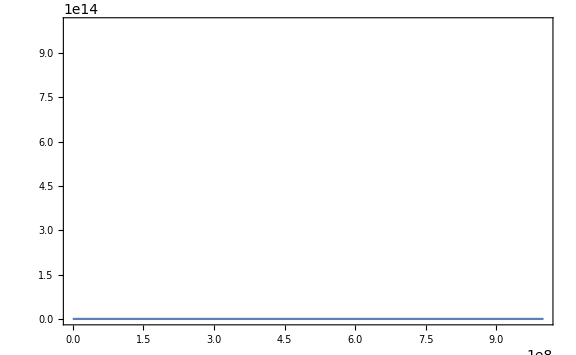

```mathematica
Plot[{(2^Log[n]), (n^2)},{n,1,1000000000}]
```

```mathematica
Log[2.]
```

0.693147

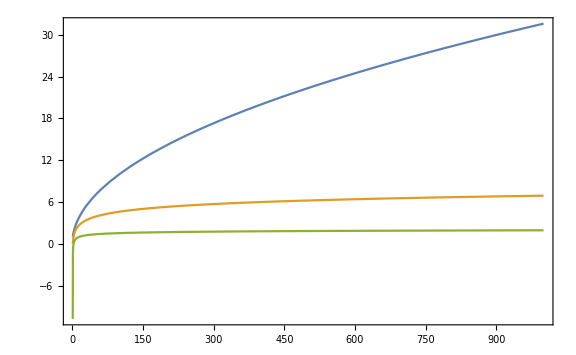

```mathematica
Plot[{√n,Log[n],Log[Log[n]] },{n,1,1000}]
```

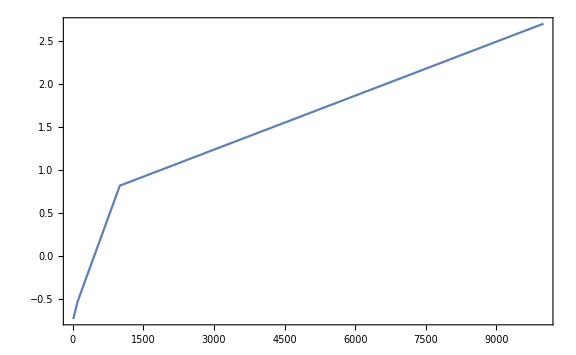

```mathematica
nvec = {10,100,1000,10000};
tvec = {0.183, 0.289, 6.541, 504.825};
ListPlot[Transpose[{nvec,Log10[tvec]}],Joined->True]
```

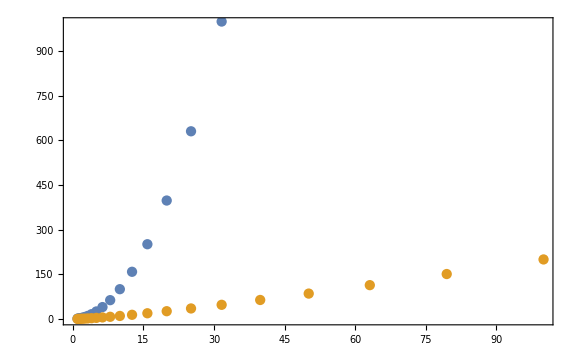

```mathematica
nvec = Table[10^n,{n,0,2,0.1}];
tvec2 = Table[n^2,{n,nvec}];
tveclog = Table[n*Log10[n],{n,nvec}];
ListPlot[{Transpose[{nvec,tvec2}],Transpose[{nvec,tveclog}]}]
```